```mathematica
ClearAll;
Get["Documents/QCDxdQCD/Mathematica/Packages/Beta'.m"]

norm={1/(4*Pi),1/(4*Pi)};
model = {3,3,6,0,0,0,0,3};
coeff = c@@Join[norm,model]
```

ClearAll

{-11/(4 π),7/(8 π^2),3/π^2,-19/(4 π),-69/(8 π^2),3/π^2}

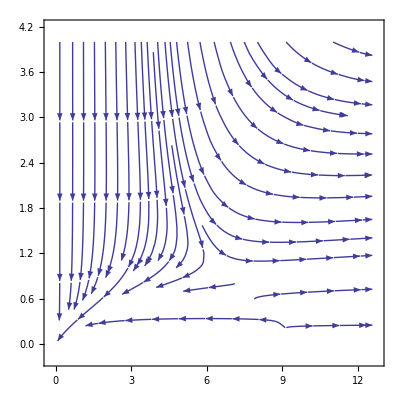

```mathematica
StreamPlot[{b1@@Join[{a1,a2},coeff],b2@@Join[{a1,a2},coeff]},{a1,0,4*Pi},{a2,0,4},StreamPoints->30]
```